dp/dt = r_P p(1-p/K_p)-β_P cp - β_int cnp
dn/dt = r_n n(1-n/K_n)-β_n cn - αnp

Solutions of the above two equations with respect to bile salt concentration are the following :

Parameter Values :

```mathematica
Subscript[r, p]=1.0 ;
Subscript[K, p]=1.3 10^8 ;
Subscript[r, n]=0.4 ;
Subscript[K, n]=3.7 10^8 ;
α=7 10^-9;
Subscript[β, p]=11 ;
Subscript[β, int]=1 10^-9 ;
Subscript[β, n]=5 ;
po=2.7 10^6 ;   
no=6 10^7     ;
```

Solution :

```mathematica
sol=ParametricNDSolve[{p'[t]==Subscript[r, p]*p[t](1-(p[t]/Subscript[K, p])) -Subscript[β, p]*c*p[t] -Subscript[β, int]*c*p[t]*n[t],n'[t]==Subscript[r, n]*n[t]*(1-(n[t]/Subscript[K, n]))-α*n[t]*p[t] -Subscript[β, n]*c*n[t], p[0]==po, n[0]==no},{p,n},{t,0,24},{c}] ;
```

Plotting of the solutions :

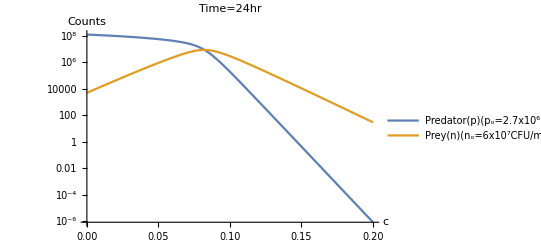

```mathematica
Plt=LogPlot[{Evaluate[{p[c][24],n[c][24]} /.sol]},{c,0,0.2},PlotStyle->Automatic,PlotLegends->LineLegend[{"Predator(p)(p_o=2.7x10^6 CFU/ml)","Prey(n)(n_o=6x10^7CFU/ml)"}],AxesLabel->{c ,Counts},PlotLabel->Style["Time=24hr",FontSize->15]]
```